```mathematica
homdirectory="/Users/keitokiddo/VC";
SetDirectory[homdirectory];
```

```mathematica
alpha=4;
l=8;
multiplicity=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
w[l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
Nbyfirst[x_]:=First[x]^-1 x
Nbysum[x_]:=Total[x]^-1 x
labelfigs[figs_]:=Table[
Labeled[figs[[i]],Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica",FontSize->fontsize],{{Top,Left}}],
{i,Length[figs]}
]
```

```mathematica
fontsize=18;
fstyle=Table[{GrayLevel[.3],Thickness[.006]},4];
```

```mathematica
(*Choose lambdas*)
a0=12;
a1=1.5;
a2=0.8;
loglambsfit=Table[a0/(1 + Exp[ a1 (x - a2)]) ,{x,l}];
lambdascorrected=Nbyfirst@(Exp[loglambsfit] - .99);
lambdasproper=PadLeft[lambdascorrected,l+1];
```

## Figure2

#### Wk

```mathematica
colorlist1=Partition[{240,249,232,
186,228,188,
123,204,196,
67,162,202,
8,104,172},3]/255;
```

```mathematica
colorlist1=Partition[{215,25,28,
253,174,97,
255,255,191,
171,217,233,
44,123,182},3]/255;
```

```mathematica
colorlist1=Partition[{208,209,230,
166,189,219,
116,169,207,
43,140,190,
4,90,141},3]/255;
```

```mathematica
colors1=RGBColor/@colorlist1//Reverse
```

{RGBColor[{Rational[4, 255], Rational[6, 17], Rational[47, 85]}],RGBColor[{Rational[43, 255], Rational[28, 51], Rational[38, 51]}],RGBColor[{Rational[116, 255], Rational[169, 255], Rational[69, 85]}],RGBColor[{Rational[166, 255], Rational[63, 85], Rational[73, 85]}],RGBColor[{Rational[208, 255], Rational[209, 255], Rational[46, 51]}]}

```mathematica
wklabs1=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"1st order", "2nd order", "3rd order", "4th order", "5th order"};
wklabs2=Style[#,FontFamily->"Helvetica",FontSize->14]&/@{"6th order", "7th order", "8th order"};
```

```mathematica
wkdamp=Transpose@Join[ConstantArray[0,{2,7}],Transpose@Table[w[6, k,d],{d,0,l-2},{k,0,l-2}]];
```

```mathematica
Do[wkdamp[[All,k]]=wkdamp[[All,k]]/wkdamp[[1,k]],{k,3,l+1}]
```

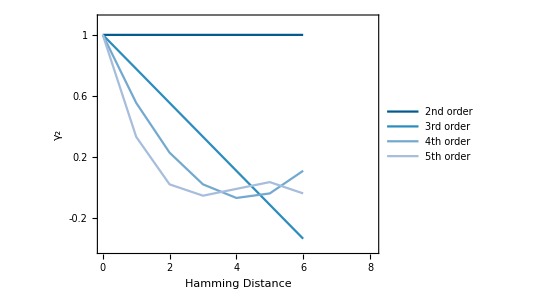

```mathematica
figWcor=Show[ListLinePlot[Transpose[wkdamp][[3;;6]],
DataRange->{0,l-2},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors1,
PlotRange->{{0,8+.1},{-.4,1.1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
Method->{"AxesInFront"->False},
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs1[[2;;]],LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}]
]]
```

```mathematica
colorlist2=Partition[{224,236,244,
158,188,218,
136,86,167},3]/255;
```

```mathematica
colorlist2=Partition[{237,248,251,
178,226,226,
102,194,164,
35,139,69},3]/255;
```

```mathematica
colors2=RGBColor/@colorlist2//Reverse
```

{RGBColor[{Rational[7, 51], Rational[139, 255], Rational[23, 85]}],RGBColor[{Rational[2, 5], Rational[194, 255], Rational[164, 255]}],RGBColor[{Rational[178, 255], Rational[226, 255], Rational[226, 255]}],RGBColor[{Rational[79, 85], Rational[248, 255], Rational[251, 255]}]}

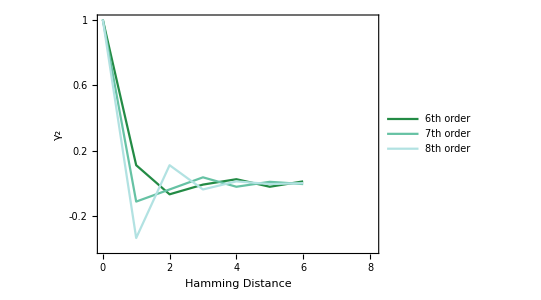

```mathematica
figWanticor=ListLinePlot[Transpose[wkdamp][[7;;]],
DataRange->{0,l-2},
BaseStyle->{FontSize->fontsize},
PlotStyle->colors2,
PlotRange->{{0,8+.1},{-.4,1}},
ImageSize->400,
AspectRatio->.75,
Frame->True,
FrameStyle->fstyle,
AxesStyle->Directive[Gray,Dashed],
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,wklabs2,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.8,.6}]
]
```

### rho

Panel C: 
rho: dots = black, connectors: gray, wk: some other color shaded wrt the weights

```mathematica
purple=RGBColor[{117,112,179}/255]
```

RGBColor[{Rational[39, 85], Rational[112, 255], Rational[179, 255]}]

```mathematica
k0=2;
```

```mathematica
G2=Table[w[l-k0,k,d],{d,0,l-k0},{k,0,l-k0}].lambdasproper[[k0 +1;;]];
```

```mathematica
vc2=Nbysum[lambdasproper[[3;;]]*Table[Binomial[l-k0,k](alpha-1)^k, {k,0,l-k0}]]
```

{0.0506906,0.11008,0.171852,0.196277,0.204475,0.182423,0.0842026}

```mathematica
vc2t=NumberForm[Round[#,.01],{2,2}]&/@Nbysum[lambdasproper[[3;;]]*Table[Binomial[l-k0,k](alpha-1)^k, {k,0,l-k0}]]
```

{0.05,0.11,0.17,0.20,0.20,0.18,0.08}

```mathematica
texts={"1st order (w=","2nd order (w=", "3rd order (w=","4th order (w=","5th order (w=", "6th order (w=", "7th order (w=", "8th order (w="};
labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[StringJoin[texts[[i+1]], ToString[vc2t[[i]]],")"],{i,7}];
ps=Table[{Black,Opacity[vc2[[i]]]},{i,Length[vc2]}];
```

```mathematica
ps=Table[{Black,Opacity[vc2[[i]]]},{i,Length[vc2]}];
```

```mathematica
texts={"1st order","2nd order", "3rd order","4th order","5th order", "6th order", "7th order", "8th order"};
labs=Style[#,FontSize->12, FontFamily->"Helvetica"]&/@Table[texts[[k+1]]<>" ("<>ToString[Subscript["v",ToString[k]],StandardForm]<>"="<>ToString[vc2t[[k]]]<>")",{k,7}];
```

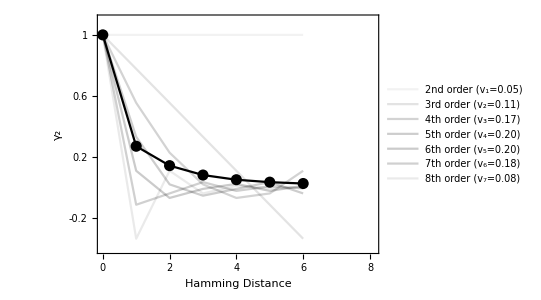

```mathematica
plotdat=Transpose@{Range[0,l-k0],Nbyfirst[G2]};
figrho2=Show[
ListLinePlot[Transpose[wkdamp][[k0+1;;]],
DataRange->{0,l-2},
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->ps,
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.1},{-.4,1.1}},
PlotRangeClipping->False,
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotLegends->Placed[LineLegend[Automatic,labs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.1,LegendMargins->0,Alignment->Right],{.78,.6}]
],
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],2]},FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
PlotStyle->GrayLevel[0],
BaseStyle->{FontSize->fontsize},
AspectRatio->.75,
PlotRange->All],
ListPlot[
plotdat,
PlotStyle->{Black,PointSize[.02]}
]
]
```

```mathematica
Gamma2s=Grid[{labelfigs[{figWcor,figWanticor,figrho2}]},Spacings->{3, 1}]
```

-Graphics-A | -Graphics-B | -Graphics-C

```mathematica
Export["figures/Gamma_2_by_k.pdf",Gamma2s];
```